```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/00_SplinePack-034.nb"]//Quiet;

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"]//Quiet;

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"]//Quiet;
```

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

```mathematica
Clear[e,f,F,G,h,M,n,P,p,Q,q,R,s,μ,σ]
```

```mathematica
{M,G,h} = Get[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20241123-01/Fig/TaskPlots/P-s/Speaking.dat"];
```

```mathematica
n =   Length[M]
μ = First/@M
σ =   Last/@M
OrderedQ[μ]
```

41

{-306.,-260.,-245.,-175.,-164.,-144.,-137.,-121.,-80.,-79.,-3.,5.,7.,9.,16.,22.,56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.,1605.,1671.}

{348.,312.,356.,294.,319.,175.,198.,140.,174.,366.,148.,203.,67.,191.,189.,100.,307.,92.,253.,94.,256.,409.,114.,327.,191.,215.,209.,163.,227.,187.,161.,123.,229.,162.,384.,151.,296.,128.,152.,305.,207.}

True

```mathematica
Q = LogNormalDistribution[e,s];
startpar = FindDistributionParameters[Select[μ,Positive],Q];
p = N[Range[n]/(1+n)];
q = Quantile[Q,p];
f = μ-q;
f /= σ;
f = f.f;
f = FindMinimum[f,List@@@startpar];
Q = Q/.Last[f];
```

Measurement | TaskPlots
P-s
Speaking
n | 41
p-value (χ^2) | 0.0003097
Distribution | LogNormalDistribution[4.90851,1.30667]
Mode | 24.56
Median | 135.437
Mean | 318.047
Quartiles | 56.102
135.437
326.961
StandardDeviation | 675.768

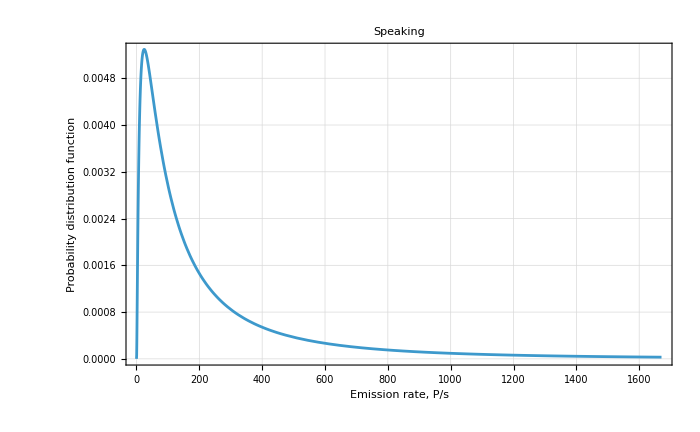

```mathematica
P = {Median,Mean,Quartiles,StandardDeviation};
P = Rule@@@Transpose[{ToString/@P,Map[#[Q]&,P]}];
PrependTo[P,"Mode"->("Median"^3/"Mean"^2)/.P];                                      (*    gilt nur für die LogNormalVerteilung    *)
PrependTo[P,"Distribution"->Q];
PrependTo[P,"p-value (χ^2)"->CDF[ChiSquareDistribution[n-2],First[f]]];
PrependTo[P,"n"->n];
PrependTo[P,"Measurement"->(taskname=Take[StringSplit[F,{".","/"}],{-4,-2}])];
TableForm[List@@@P]

Plot[
PDF[Q,x],{x,0,Last[μ]},
Frame->True,
FrameLabel->{Last[FrameLabel/.Rest[List@@G]],"Probability distribution function"},
GridLines->Automatic,
ImageSize->700,
LabelStyle->{
FontColor->GrayLevel[0],
FontFamily->"Lucida Sans Unicode",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->14},
PlotLabel->Last["Measurement"/.P],
PlotRange->All]
```

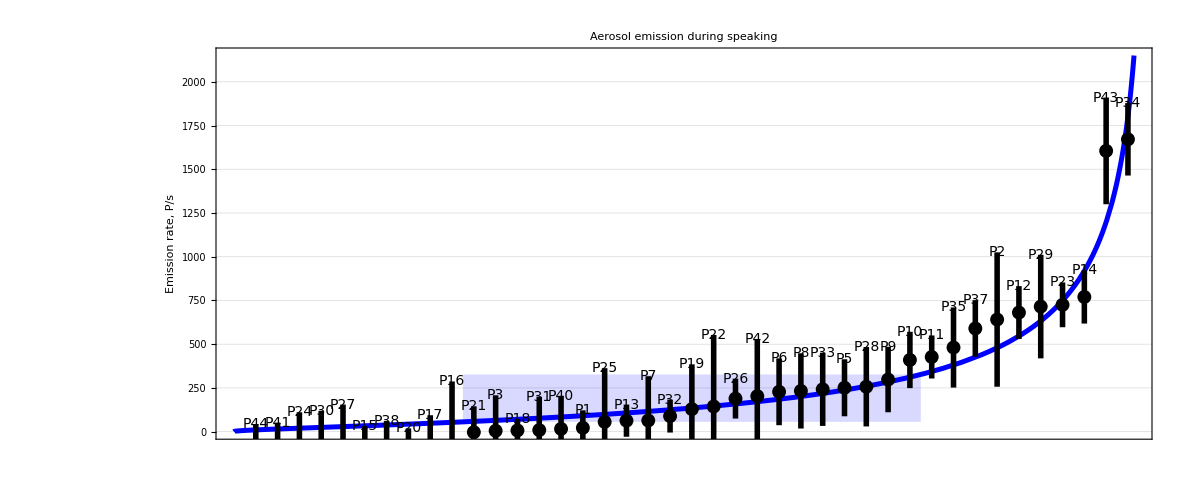

```mathematica
Clear[f];
f[k_] := Quantile[Q,k/(1+n)];
L = Plot[f[x],{x,0,n+1},DisplayFunction->Identity,PlotRange->(PlotRange/.Rest[List@@G])];
L = Extract[L,Most[First[Position[L,Line]]]];
R = Transpose[{(1+n)*{1,3}/4.,("Quartiles"/.P)[[{1,3}]]}];
h = ReplacePart[G,
Prepend[G[[1]],
{Blue,
{Opacity[0.15],Rectangle@@R},
{Thickness[0.003],L}}
],1];
h = h/.{
"Arial"->"Lucida Sans Unicode",
(FontSize -> 16)->(FontSize -> 14)}
```

```mathematica
Export[StringJoin[NotebookDirectory[],"\\output directory\\","Speaking","_lognormal.svg"],h]
```

C:\Users\mona_\Downloads\upload aerosol study 2020\\output directory\Speaking_lognormal.svg

```mathematica
(*

ENDE

*)
```

```mathematica
Clear[L,k,n]
```

```mathematica
L = p^k*(1-p)^(1+n-k)
```

(1-p)^(1-k+n) p^k

```mathematica
Solve[D[Log[L],p]/L==0,p]
```

{{p→ConditionalExpression[0, Re[k]<-1]},{p→ConditionalExpression[1, Re[n]<-2+Re[k]]},{p→k/(1+n)}}